# Test how well a gamma distribution fits the luminosity distribution of virtual packets

### Load data from two 1D arrays into one 2D array. All energies/luminosities are positive; i.e., all packets leave the supernova. No filtering needed.

```mathematica
SetDirectory[NotebookDirectory[]];
data=Transpose[Import["virt_packets.hdf5", {"Datasets", {"/virt_packet_nus/values", "/virt_packet_energies/values"}}]];
data[[All,1]]=3 10^8*10^10/data[[All,1]];
Dimensions[data]
```

{3137.84,3132.11,3112.8,3101.93,3094.21,3083.61,3066.58,3054.71,3048.03,3032.24,3228.37,3208.15,3204.72,3186.61,3156.09,3131.21,3122.59,3089.5,2679465,7437.47,7398.19,7372.49,7343.13,7324.33,7299.34,7275.25,7644.58,7609.41,7554.52,7512.57,7496.75,7426.17,7415.61,7350.32,7311.16,7303.93}
 |  |  |  |

{2679500,2}

```mathematica
sortedData=SortBy[data,First];
(* transpose gives list with two sublist, the ν and L, WeightedData expects two separate lists, so use Apply=@@ *)wd=WeightedData@@Transpose[data];
MinMax[wd["InputData"]]
binWidth=(%[[2]]-%[[1]])/1000
MinMax[data[[All,2]]]
lmax=%[[2]];
```

{516.279,228126.}

227.61

{4.67523×10^-56,1.32096×10^-6}

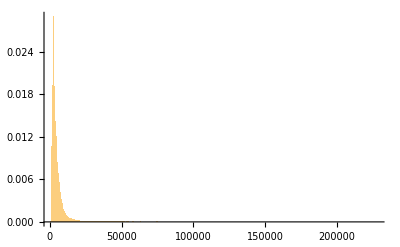

```mathematica
Histogram[wd, 2000]
```

## Rescale a window of samples

### the distributions seem to have multiple modes and look very different depending on frequency. It seems the individual absorption lines are visible. No hope of an accurate description by Gamma or Beta distributions

{0.00429658,0.00440363}

{5.66633×10^-53,9.31946×10^-7}

FindRoot::jsing: Encountered a singular Jacobian at the point {α, β} = {1., 1.09951×10^12}. Try perturbing the initial point(s).

{α→1.,β→1.09951×10^12}

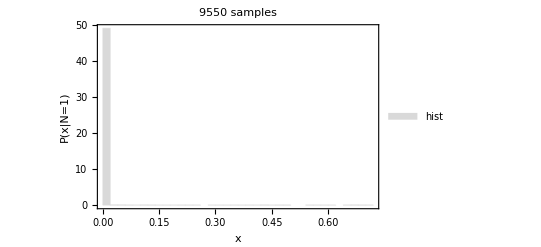

{1.09951×10^12,1.20993975434921988892698432925505329919696`15.954589770191005*^-336889118221}

```mathematica
nmin=24700;nmax=nmin+9549;
{sortedData[[nmin,1]],sortedData[[nmax,1]]}/ Max[sortedData[[All,1]]]
samples=sortedData[[nmin;;nmax,2]];
(*samples /=Max[sortedData[[;;,2]]](1+10^-6);*)
Print[MinMax[samples]];
samples /=lmax;
gammaDist=GammaDistribution[α,1/β];
pars=FindDistributionParameters[samples, gammaDist,
ParameterEstimator->"MethodOfMoments"]
(*ParameterEstimator->"MaximumLikelihood"]*)
(*gammaDist=gammaDist/.{α->1.5551,β->72.5};*)
gammaDist=gammaDist/.pars;
Show[Legended[Histogram[samples,25,"ProbabilityDensity",Frame->True, FrameLabel-> {"x","P(x|N=1)"}, PlotLabel->ToString[Length[samples]]<>" samples",ChartStyle->LightGray],SwatchLegend[{LightGray},{"hist"}]]
(*,
Legended[Plot[PDF[gammaDist,x],{x,0,Max[samples]},PlotStyle->{Red,Thick,Dashed},PlotRange->Full],LineLegend[{Directive[Red,Thick,Dashed]},{"Gamma(x|ϕ^*)"}]],
Legended[SmoothHistogram[samples,PlotRange->Full,PlotStyle->Blue],LineLegend[{Directive[Blue]},{"KDE"}]]
*)]
Export["gamma.pdf", %];
PDF[gammaDist,MinMax[samples]]
```

```mathematica
Table[Moment[samples,i],{i,1,2}]
Moment[samples,#]&/@ {1,2}
```

{0.365087,0.194894}

{0.365087,0.194894}

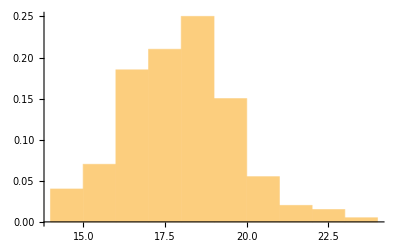

```mathematica
With[{nsum=50},
Histogram[Take[ListConvolve[Table[1,{i,nsum}],samples],{1,-1,nsum}],"Scott","PDF"]
]
```

```mathematica
Table[1,{i,4}],samples],{1,-1,4}]
```

```mathematica
ListConvolve[{1,1},{1,2,3,4,5}]
```

{3,5,7,9}

## Poisson posterior from Aggarwal & Caldwell

```mathematica
Assuming[n≥ 0&&n∈Integers,Integrate[(2^(2n) n!)/(√π (2n)!)λ^(n-1/2)Exp[-λ]//Simplify,{λ,0,∞}]]
```

1

```mathematica
1/s PDF[PoissonDistribution[a^2/b λ],x/s]/.s->b/a//Simplify
```

Piecewise[{{(a ⅇ^(-(a^2 λ)/b) ((a^2 λ)/b)^((a x)/b))/(b (a x)/b!), (a x)/b≥0}, {0, True}}]

```mathematica
Assuming[a>0&&b>0&&n≥ 0&&x≥ 0,Integrate[(1/s PDF[PoissonDistribution[a^2/b λ],x/s]/.s->b/a) (2^(2n) n!)/(√π (2n)!)λ^(n-1/2)Exp[-λ],{λ,0,∞}]]//Simplify
```

(a^(1+(2 a x)/b) b^(-1/2+n) (a^2+b)^(-1/2-n-(a x)/b) Gamma[1/2+n+(a x)/b])/(Gamma[1/2+n] Gamma[1+(a x)/b])

```mathematica
(4^n a (a^2/b)^((a x)/b) ((a^2+b)/b)^(-1/2-n-(a x)/b) n! Gamma[1/2+n+(a x)/b])/(b π (2 n)! ((a x)/b)!)/.b->s a//Simplify
```

(4^n (a/s)^(x/s) ((a+s)/s)^(-1/2-n-x/s) n! Gamma[1/2+n+x/s])/(π s (2 n)! x/s!)

## Scaled Poisson distribution a la Zech for discrete x

80.5598

1.

{80.5598,80.9688}

{6.08266,7.68137}

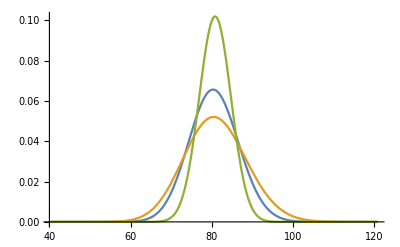

```mathematica
scaled[x_,λ_,a_,b_]:=(a ⅇ^(-(a^2 λ)/b) ((a^2 λ)/b)^((a x)/b))/(b ((a x)/b)!)
scaledN[x_,n_,a_,b_]:=(a^(1+(2 a x)/b) b^(-1/2+n) (a^2+b)^(-1/2-n-(a x)/b) Gamma[1/2+n+(a x)/b])/(Gamma[1/2+n] Gamma[1+(a x)/b])
```

```mathematica
Total[samples]
```

89.9498

```mathematica
Grad[Log[scaledN[x,Subscript[n, b],a,b]],{a,b}]//Simplify
```

{1/(a b (a^2+b))(b^2+2 a b x+2 a^3 x Log[a]+2 a b x Log[a]-a^3 x Log[a^2+b]-a b x Log[a^2+b]-a (a^2+b) x PolyGamma[0,1+(a x)/b]+a^3 x PolyGamma[0,1/2+(a x)/b+n_b]+a b x PolyGamma[0,1/2+(a x)/b+n_b]-2 a^2 b n_b),-1/(2 b^2 (a^2+b))(a^2 b+2 b^2+2 a b x+4 a^3 x Log[a]+4 a b x Log[a]-2 a^3 x Log[a^2+b]-2 a b x Log[a^2+b]-2 a^3 x PolyGamma[0,1+(a x)/b]-2 a b x PolyGamma[0,1+(a x)/b]+2 a^3 x PolyGamma[0,1/2+(a x)/b+n_b]+2 a b x PolyGamma[0,1/2+(a x)/b+n_b]-2 a^2 b n_b-2 b^2 (a^2+b) (Log[b]-Log[a^2+b]-PolyGamma[0,1/2+n_b]+PolyGamma[0,1/2+(a x)/b+n_b]) Subscript^(0,1)[n,b])}

```mathematica
Simplify[-D[Grad[Log[scaledN[x,Subscript[n, b],a,b]],{a,b}],{{a,b}}]];
```

Variance

```mathematica
NIntegrate[scaled[x,λ,a,b]x,{x,0,∞}]
```

NIntegrate::inumr: The integrand a\ ⅇ^-a^2\ λ/b\ x\ (a^2\ λ/b)^a\ x/b/b\ a\ x/b ! has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞, 0.}}.

NIntegrate[scaled[x,λ,a,b] x,{x,0,∞}]

## Reference posterior for normal unknown mean and variance

ⅇ^(-(n (-first^2+second+(first-μ)^2))/(2 (b-μ^2))) (b-μ^2)^(-1-n/2)

(ⅇ^(-(150 (0.0511236+(0.2694-μ)^2))/(b-μ^2)))/((b-μ^2)^151)

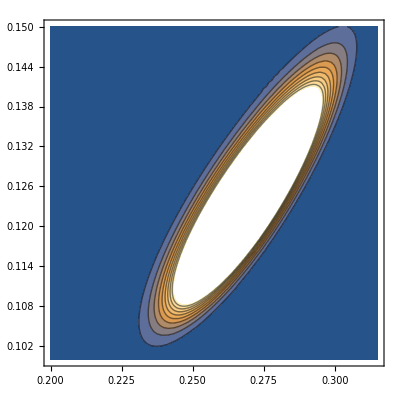

```mathematica
refPost[μ_,b_,n_,firstMom_, secMom_]:=(b-μ^2)^(-1-n/2)Exp[-n/(2 (b-μ^2))((secMom-firstMom^2)+(firstMom-μ)^2)]
refPost[μ,b,n,first,second]
refPost[μ,b,300,0.2694,0.1237]
ContourPlot[refPost[μ,b,300,0.2694,0.1237],{μ,0.2,0.315},{b,0.1,0.15}]
```

NOrmalization constant

```mathematica
norm[n_,νn_,κn_,σn_,ν0_,κ0_,σ0_]:=Gamma[νn/2]/Gamma[ν0/2] √(κ0/κn)((ν0 σ0^2)^(ν0/2))/((νn σn^2)^(νn/2))1/Pi^(n/2)
normRef[n_,νn_,κn_,σn_]:=Gamma[νn/2]/Gamma[-1/2] √(κ0/κn)((ν0 σ0^2)^(ν0/2))/((νn σn^2)^(νn/2))1/Pi^(n/2)
norm[n,n-1,n,σn,-1,0,0]
```

Power::infy: Infinite expression 1/√0 encountered.

Infinity::indet: Indeterminate expression -0\ π^-n/2\ ComplexInfinity\ Gamma[1/2\ (-1 + n)]/2\ √π encountered.

Indeterminate

No solution found in minutes

```mathematica
(*Integrate[scaledN[x,n,μ,b] refPost[μ,b,300,0.2694,0.1237],{μ,-∞,∞},{b,0,∞}]*)
```

$Aborted

Numerical integration for comparison to Laplace

```mathematica
prob[x_,n_,x1_,x2_]:=Module[{hessian, sol,expr,a,b},
expr=scaledN[x,n,a,b]refPost[a,b,n,x1,x2];
hessian=-D[Grad[Log[expr],{a,b}],{{a,b}}];
sol=FindMaximum[{Log[expr],a>0&&b>a^2},{{a,x1},{b,x2}}];
√((2 Pi)^2/(Det[hessian]/.sol[[2]]))Exp[sol[[1]]]
]
prob[100,Length[samples], Moment[samples,1],Moment[samples,2]]
```

## Compare the distributions

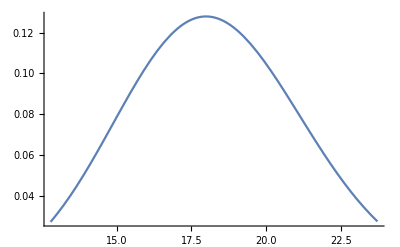

```mathematica
Block[{x1=Moment[samples,1](*0.2694468856871592*),x2=Moment[samples,2](*0.12374921066530022*),n=Length[samples],means,seconds,std,λ,points,xmin, xmax,axes},
λ=n;
xmin=0.7 λ x1;
xmax = 1.3 λ x1;
(*Print[λ a];
Print[NIntegrate[scaledN[x,n,a,b],{x,0,∞}]];
means=NIntegrate[{x scaled[x,λ,a,b],x scaledN[x,n,a,b]},{x,0,∞}];
seconds=NIntegrate[{x^2 scaled[x,λ,a,b],x^2 scaledN[x,n,a,b]},{x,0,∞}];
std=√(seconds-means^2);
Print[means];
Print[std];*)
points=Table[{x,prob[x,n,x1,x2]},{x,xmin,xmax,1}];
axes={True,False};
GraphicsColumn[{ListPlot[points,Axes->axes],Plot[{scaled[x,λ,x1,x2](*,scaledN[x,n,x1,x2],PDF[NormalDistribution[n x1,Sqrt[n (x2-x1^2)]],x]*)},{x,Max[0,xmin],xmax},Axes->axes]}
]
]
```

{295.959,{a→0.270124,b→0.123734}}

1.02518×10^125

General::unfl: Underflow occurred in computation.

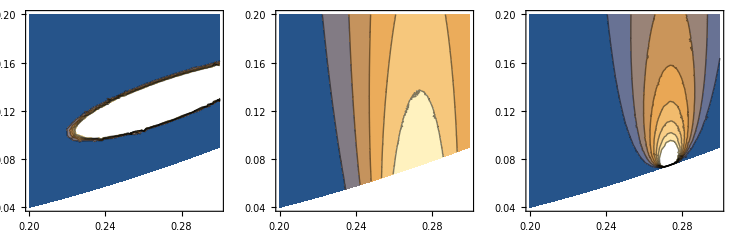

```mathematica
Block[{n=300,x1=0.2694468856871592,x2=0.12374921066530022,x=82,expr=scaledN[x,n,a,b]refPost[a,b,n,x1,x2],
hessian,sol,integral,region},
hessian=-D[Grad[Log[expr],{a,b}],{{a,b}}];
(*NIntegrate[expr,{a,0.2,0.35},{b,0.1,0.2}];*)
(*Simplify[-D[Grad[Log[expr],{a,b}],{{a,b}}]]//TraditionalForm*)
sol=FindMaximum[{Log[expr],a>0&&b>a^2},{{a,0.1},{b,0.1}}];
Print[sol];
integral=√((2 Pi)^2/(Det[hessian]/.sol[[2]]))Exp[sol[[1]]];
Print[integral];
region=ImplicitRegion[a>0.2&&a<0.3&&b>0.01&&b<0.2&&b>a^2,{a,b}];
GraphicsRow[ContourPlot[#,{a,b}∈region]&/@{expr,scaledN[x,n,a,b],PDF[NormalDistribution[n a,√(n(b-a^2))],x]}
]
]
```

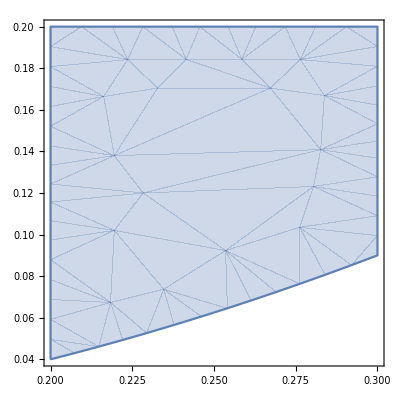

```mathematica
RegionPlot[
```

Try Laplace

```mathematica
Simplify[-D[Grad[Log[refPost[a,b,n,x1,x2]],{a,b}],{{a,b}}]]//TraditionalForm
```

((-(n+2) a^4+2 n x1 a^3-3 n (b+x2) a^2+6 b n x1 a+b (2 b-n x2))/((a^2-b)^3) | -(-2 (n+1) a^3+3 n x1 a^2+2 (b-n x2) a+b n x1)/((a^2-b)^3)
-(-2 (n+1) a^3+3 n x1 a^2+2 (b-n x2) a+b n x1)/((a^2-b)^3) | (-(3 n+2) a^2+4 n x1 a+b (n+2)-2 n x2)/(2 (a^2-b)^3))

```mathematica
{0.12341/0.12374921066530022,300/299.}
```

{0.997259,1.00334}